```mathematica
(* Subscript[I, 2](l,L) at 2 T_c with free b.c.
=c/2 ln[(f(l/L) f((L-l)/L))/(√L f(1))]
where f(x)=Dedekindeta(ix) *)
```

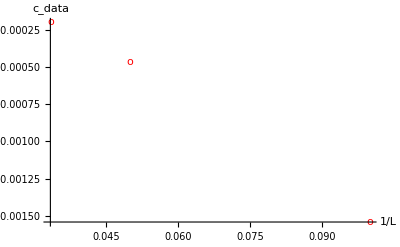

```mathematica
SetDirectory[NotebookDirectory[]];
(********************Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]********************)
Clear[data,datalin,col1,col2,l];
data=Sort[Import["extra_x0.400000_D1.880000_T2.000000.dat","Table"]];
col1=data[[;;,4]];
col2=data[[;;,5]];
datalin=Table[{col1[[i]],col2[[i]]},{i,1,Length[col1]}];
ListPlot[datalin,AxesLabel->{"1/L","c_data"},PlotStyle->{Red},PlotMarkers->{"o",Large},PlotRange->All]
```

{0.0625,0.041667,0.03125}

{-0.06166,-0.041029,-0.02168}

{{0.0625,-0.06166},{0.041667,-0.041029},{0.03125,-0.02168}}

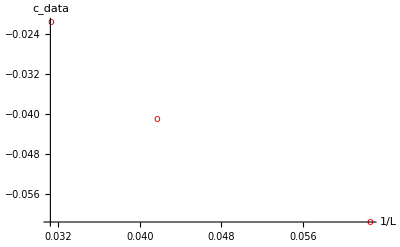

```mathematica
SetDirectory[NotebookDirectory[]];
(********************Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]********************)
Clear[data,datalin,col1,col2,l];
(*data=Sort[Import["cval_D1.900_T1.120.dat","Table"],#1[[1]]<#2[[1]]&];*)
data=Sort[Import["extra_x0.125000_D1.880000_T2.000000.dat","Table"]];
col1=data[[;;,4]]
col2=data[[;;,5]]
datalin=Table[{col1[[i]],col2[[i]]},{i,1,Length[col1]}]
ListPlot[datalin,AxesLabel->{"1/L","c_data"},PlotStyle->{Red},PlotMarkers->{"o",Large},PlotRange->All]
```

{0.055556,0.041667,0.033333}

{-0.027734,-0.017522,-0.0099123}

{{0.055556,-0.027734},{0.041667,-0.017522},{0.033333,-0.0099123}}

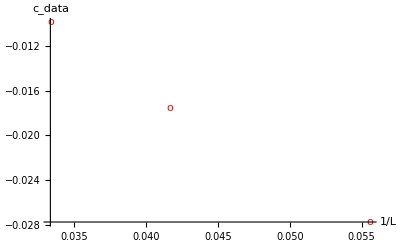

```mathematica
SetDirectory[NotebookDirectory[]];
(********************Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]********************)
Clear[data,datalin,col1,col2,l];
(*data=Sort[Import["cval_D1.900_T1.120.dat","Table"],#1[[1]]<#2[[1]]&];*)
data=Sort[Import["extra_x0.166670_D1.880000_T2.000000.dat","Table"]];
col1=data[[;;,4]]
col2=data[[;;,5]]
datalin=Table[{col1[[i]],col2[[i]]},{i,1,Length[col1]}]
ListPlot[datalin,AxesLabel->{"1/L","c_data"},PlotStyle->{Red},PlotMarkers->{"o",Large},PlotRange->All]
```